```mathematica
(*https://www.wolframcloud.com/objects/demonstrations/MusicBoxToyWithElementaryCellularAutomata-source.nb*)
```

```mathematica
rule=105
```

105

```mathematica
cells=5
```

5

```mathematica
generations=16
```

16

```mathematica
SeedRandom
```

SeedRandom

```mathematica
all1dca = Table[CellularAutomaton[105,IntegerDigits[seed,2,cells ],generations-1], {seed,0,(2^cells)-1}];
```

```mathematica
aa=Flatten[Table[Mod[Table[FromDigits[all1dca[[j, k]],2], {j,1,2^cells}],5], {k,2,8}]]
```

{1,2,4,1,2,2,2,0,3,1,4,3,3,0,0,0,1,1,1,3,3,2,0,3,1,4,4,4,0,2,4,0,0,3,1,3,1,4,0,2,1,1,2,3,0,4,4,4,2,2,2,1,3,4,0,0,4,1,2,0,3,0,3,1,1,0,4,3,2,1,0,4,3,2,1,0,4,3,2,1,0,4,3,2,1,0,4,3,2,1,0,4,3,2,1,0,0,4,2,0,4,4,4,1,3,0,2,3,3,1,1,1,0,0,0,3,3,4,1,3,0,2,2,2,1,4,2,1,1,3,0,3,0,2,1,4,0,0,4,3,1,2,2,2,4,4,4,0,3,2,1,1,2,0,4,1,3,1,3,0,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,1,2,4,1,2,2,2,0,3,1,4,3,3,0,0,0,1,1,1,3,3,2,0,3,1,4,4,4,0,2,4,0}

```mathematica
Length[%]
```

224

```mathematica
(* second chord transform*)
```

```mathematica
(* pentatonic:BlackKeys{Db,Eb,Gb,Ab,Bb}*)
```

```mathematica
(*Cminor:https://www.pianoscales.org/pentatonic.html*)
```

```mathematica
v={1,3,6,8,10,1,3,6,8,10}
```

{1,3,6,8,10,1,3,6,8,10}

```mathematica
PiDigits=Table[v[[aa[[i]]]],{i,Length[aa]}]
```

{1,3,8,1,3,3,3,List,6,1,8,6,6,List,List,List,1,1,1,6,6,3,List,6,1,8,8,8,List,3,8,List,List,6,1,6,1,8,List,3,1,1,3,6,List,8,8,8,3,3,3,1,6,8,List,List,8,1,3,List,6,List,6,1,1,List,8,6,3,1,List,8,6,3,1,List,8,6,3,1,List,8,6,3,1,List,8,6,3,1,List,8,6,3,1,List,List,8,3,List,8,8,8,1,6,List,3,6,6,1,1,1,List,List,List,6,6,8,1,6,List,3,3,3,1,8,3,1,1,6,List,6,List,3,1,8,List,List,8,6,1,3,3,3,8,8,8,List,6,3,1,1,3,List,8,1,6,1,6,List,List,1,3,6,8,List,1,3,6,8,List,1,3,6,8,List,1,3,6,8,List,1,3,6,8,List,1,3,6,8,List,1,1,3,8,1,3,3,3,List,6,1,8,6,6,List,List,List,1,1,1,6,6,3,List,6,1,8,8,8,List,3,8,List}

```mathematica
SeedRandom[123]
```

RandomGeneratorState[…]

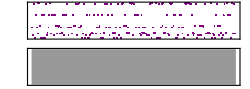

CellularAutomata-105_level7_BlackKeys_1.mid

```mathematica
snd1=Sound[Table[SoundNote[RandomChoice[{"HighWoodblock","Snare","Sticks","SideStick","BassDrum","MidTom","LowBongo","LowTom","LowWoodblock"}],.24],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_1.mid",snd1]
```

```mathematica
snd2=Sound[Table[SoundNote[PiDigits[[i]],.24,"Piano"],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_2.mid",snd2]
```

Sound[{SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano]}]

SoundNote::invnote: "List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_2.mid

```mathematica
snd2a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,"SynthBass2"],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_2a.mid",snd2a]
```

Sound[{SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2]}]

SoundNote::invnote: "-24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_2a.mid

```mathematica
(* 8th notes*)
snd10=Sound[Table[SoundNote[PiDigits[[i]]+24,.24,"Flute"],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_10.mid",snd10]
```

Sound[{SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[30,0.24,Flute],SoundNote[25,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute],SoundNote[27,0.24,Flute],SoundNote[32,0.24,Flute],SoundNote[24+List,0.24,Flute]}]

SoundNote::invnote: "24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_10.mid

```mathematica
snd3=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,RandomChoice[If[Mod[i,5]>0,{"Bass","ElectricBass","BassAndLead","PickedBass"},{"SynthBass2"}]]],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_3.mid",snd3]
```

Sound[{SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-16,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,PickedBass],SoundNote[-21,0.24,ElectricBass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-18,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,PickedBass],SoundNote[-18,0.24,ElectricBass],SoundNote[-18,0.24,PickedBass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-23,0.24,PickedBass],SoundNote[-23,0.24,Bass],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,ElectricBass],SoundNote[-21,0.24,PickedBass],SoundNote[-24+List,0.24,PickedBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,Bass],SoundNote[-18,0.24,BassAndLead],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,PickedBass],SoundNote[-23,0.24,PickedBass],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,Bass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,BassAndLead],SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,Bass],SoundNote[-18,0.24,Bass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-16,0.24,PickedBass],SoundNote[-21,0.24,ElectricBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,Bass],SoundNote[-23,0.24,Bass],SoundNote[-18,0.24,BassAndLead],SoundNote[-16,0.24,BassAndLead],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,Bass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,BassAndLead],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-18,0.24,PickedBass],SoundNote[-23,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-16,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-21,0.24,Bass],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,PickedBass],SoundNote[-16,0.24,Bass],SoundNote[-18,0.24,BassAndLead],SoundNote[-21,0.24,Bass],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,PickedBass],SoundNote[-16,0.24,Bass],SoundNote[-18,0.24,BassAndLead],SoundNote[-21,0.24,ElectricBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-16,0.24,Bass],SoundNote[-18,0.24,Bass],SoundNote[-21,0.24,ElectricBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-16,0.24,ElectricBass],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-16,0.24,PickedBass],SoundNote[-21,0.24,Bass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,PickedBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-16,0.24,Bass],SoundNote[-23,0.24,BassAndLead],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,ElectricBass],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,PickedBass],SoundNote[-18,0.24,Bass],SoundNote[-16,0.24,Bass],SoundNote[-23,0.24,BassAndLead],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-21,0.24,ElectricBass],SoundNote[-21,0.24,Bass],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,BassAndLead],SoundNote[-21,0.24,ElectricBass],SoundNote[-23,0.24,Bass],SoundNote[-23,0.24,Bass],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,PickedBass],SoundNote[-18,0.24,Bass],SoundNote[-24+List,0.24,PickedBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,BassAndLead],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,Bass],SoundNote[-21,0.24,PickedBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,PickedBass],SoundNote[-16,0.24,ElectricBass],SoundNote[-24+List,0.24,PickedBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,PickedBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,PickedBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-23,0.24,Bass],SoundNote[-18,0.24,BassAndLead],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,PickedBass],SoundNote[-23,0.24,PickedBass],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,PickedBass],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,BassAndLead],SoundNote[-18,0.24,BassAndLead],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,PickedBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,ElectricBass],SoundNote[-18,0.24,Bass],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-23,0.24,PickedBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-18,0.24,ElectricBass],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-23,0.24,PickedBass],SoundNote[-21,0.24,ElectricBass],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-21,0.24,BassAndLead],SoundNote[-21,0.24,BassAndLead],SoundNote[-21,0.24,BassAndLead],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,PickedBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-24+List,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,ElectricBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-21,0.24,Bass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,BassAndLead],SoundNote[-23,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-16,0.24,Bass],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,PickedBass],SoundNote[-21,0.24,PickedBass],SoundNote[-16,0.24,PickedBass],SoundNote[-24+List,0.24,PickedBass]}]

SoundNote::invnote: "-24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_3.mid

```mathematica
w0={"Bass","ElectricBass","BassAndLead","PickedBass","SynthBass2"};
```

```mathematica
snd3a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,w0[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_3a.mid",snd3a]
```

Sound[{SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,Bass],SoundNote[-21,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-23,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,Bass],SoundNote[-21,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-23,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-23,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-16,0.24,ElectricBass],SoundNote[-16,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-23,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-23,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-21,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-24+List,0.24,BassAndLead],SoundNote[-24+List,0.24,PickedBass],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,Bass],SoundNote[-23,0.24,ElectricBass],SoundNote[-18,0.24,BassAndLead],SoundNote[-18,0.24,PickedBass],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,Bass],SoundNote[-18,0.24,ElectricBass],SoundNote[-23,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,Bass],SoundNote[-24+List,0.24,ElectricBass],SoundNote[-21,0.24,BassAndLead],SoundNote[-16,0.24,PickedBass],SoundNote[-24+List,0.24,SynthBass2]}]

SoundNote::invnote: "-24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_3a.mid

```mathematica
w1={"AltoSax","ElectricGuitar","Piano","Banjo","Whistle"};
```

```mathematica
snd4a=Sound[Table[SoundNote[PiDigits[[i]],.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_4a.mid",snd4a]
```

Sound[{SoundNote[1,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[1,0.24,Whistle],SoundNote[3,0.24,AltoSax],SoundNote[3,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[List,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Banjo],SoundNote[1,0.24,Whistle],SoundNote[6,0.24,AltoSax],SoundNote[6,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[List,0.24,Whistle],SoundNote[3,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[6,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[List,0.24,Whistle],SoundNote[3,0.24,AltoSax],SoundNote[1,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[3,0.24,AltoSax],SoundNote[3,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[8,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[6,0.24,ElectricGuitar],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[1,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[1,0.24,Whistle],SoundNote[6,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[1,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[List,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[6,0.24,ElectricGuitar],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[1,0.24,Whistle],SoundNote[6,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Banjo],SoundNote[1,0.24,Whistle],SoundNote[6,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[8,0.24,Whistle],SoundNote[6,0.24,AltoSax],SoundNote[1,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[8,0.24,ElectricGuitar],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[3,0.24,AltoSax],SoundNote[1,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[List,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[1,0.24,ElectricGuitar],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[1,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[6,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[6,0.24,Whistle],SoundNote[6,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Banjo],SoundNote[1,0.24,Whistle],SoundNote[1,0.24,AltoSax],SoundNote[1,0.24,ElectricGuitar],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Banjo],SoundNote[3,0.24,Whistle],SoundNote[List,0.24,AltoSax],SoundNote[6,0.24,ElectricGuitar],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[8,0.24,Whistle],SoundNote[8,0.24,AltoSax],SoundNote[List,0.24,ElectricGuitar],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Banjo],SoundNote[List,0.24,Whistle]}]

SoundNote::invnote: "List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_4a.mid

```mathematica
snd4b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_4b.mid",snd4b]
```

Sound[{SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{1,4},0.24,Whistle],SoundNote[{3,6},0.24,AltoSax],SoundNote[{3,6},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{6,9},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{List,3+List},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{1,4},0.24,Banjo],SoundNote[{1,4},0.24,Whistle],SoundNote[{6,9},0.24,AltoSax],SoundNote[{6,9},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{List,3+List},0.24,Whistle],SoundNote[{3,6},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{List,3+List},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{6,9},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{List,3+List},0.24,Whistle],SoundNote[{3,6},0.24,AltoSax],SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{3,6},0.24,AltoSax],SoundNote[{3,6},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{8,11},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{1,4},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{6,9},0.24,ElectricGuitar],SoundNote[{List,3+List},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{1,4},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{List,3+List},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{1,4},0.24,Whistle],SoundNote[{6,9},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{List,3+List},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{6,9},0.24,ElectricGuitar],SoundNote[{6,9},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{1,4},0.24,Whistle],SoundNote[{6,9},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{1,4},0.24,Banjo],SoundNote[{1,4},0.24,Whistle],SoundNote[{6,9},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{6,9},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{List,3+List},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{8,11},0.24,Whistle],SoundNote[{6,9},0.24,AltoSax],SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{8,11},0.24,ElectricGuitar],SoundNote[{8,11},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{3,6},0.24,AltoSax],SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{List,3+List},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{6,9},0.24,Piano],SoundNote[{1,4},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{1,4},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{3,6},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{6,9},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{6,9},0.24,Whistle],SoundNote[{6,9},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{List,3+List},0.24,Piano],SoundNote[{List,3+List},0.24,Banjo],SoundNote[{1,4},0.24,Whistle],SoundNote[{1,4},0.24,AltoSax],SoundNote[{1,4},0.24,ElectricGuitar],SoundNote[{6,9},0.24,Piano],SoundNote[{6,9},0.24,Banjo],SoundNote[{3,6},0.24,Whistle],SoundNote[{List,3+List},0.24,AltoSax],SoundNote[{6,9},0.24,ElectricGuitar],SoundNote[{1,4},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{8,11},0.24,Whistle],SoundNote[{8,11},0.24,AltoSax],SoundNote[{List,3+List},0.24,ElectricGuitar],SoundNote[{3,6},0.24,Piano],SoundNote[{8,11},0.24,Banjo],SoundNote[{List,3+List},0.24,Whistle]}]

SoundNote::invnote: "List" is not a valid pitch specification.

SoundNote::invnote: "3+List" is not a valid pitch specification.

SoundNote::invnote: "List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_4b.mid

```mathematica
snd5b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.48,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_5b.mid",snd5b]
(* quarter notes*)
```

Sound[{SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{1,4},0.48,Whistle],SoundNote[{3,6},0.48,AltoSax],SoundNote[{3,6},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{6,9},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{List,3+List},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{1,4},0.48,Banjo],SoundNote[{1,4},0.48,Whistle],SoundNote[{6,9},0.48,AltoSax],SoundNote[{6,9},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{List,3+List},0.48,Whistle],SoundNote[{3,6},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{List,3+List},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{6,9},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{List,3+List},0.48,Whistle],SoundNote[{3,6},0.48,AltoSax],SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{3,6},0.48,AltoSax],SoundNote[{3,6},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{8,11},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{1,4},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{6,9},0.48,ElectricGuitar],SoundNote[{List,3+List},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{1,4},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{List,3+List},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{1,4},0.48,Whistle],SoundNote[{6,9},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{List,3+List},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{6,9},0.48,ElectricGuitar],SoundNote[{6,9},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{1,4},0.48,Whistle],SoundNote[{6,9},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{1,4},0.48,Banjo],SoundNote[{1,4},0.48,Whistle],SoundNote[{6,9},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{6,9},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{List,3+List},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{8,11},0.48,Whistle],SoundNote[{6,9},0.48,AltoSax],SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{8,11},0.48,ElectricGuitar],SoundNote[{8,11},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{3,6},0.48,AltoSax],SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{List,3+List},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{6,9},0.48,Piano],SoundNote[{1,4},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{1,4},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{3,6},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{6,9},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{6,9},0.48,Whistle],SoundNote[{6,9},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{List,3+List},0.48,Piano],SoundNote[{List,3+List},0.48,Banjo],SoundNote[{1,4},0.48,Whistle],SoundNote[{1,4},0.48,AltoSax],SoundNote[{1,4},0.48,ElectricGuitar],SoundNote[{6,9},0.48,Piano],SoundNote[{6,9},0.48,Banjo],SoundNote[{3,6},0.48,Whistle],SoundNote[{List,3+List},0.48,AltoSax],SoundNote[{6,9},0.48,ElectricGuitar],SoundNote[{1,4},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{8,11},0.48,Whistle],SoundNote[{8,11},0.48,AltoSax],SoundNote[{List,3+List},0.48,ElectricGuitar],SoundNote[{3,6},0.48,Piano],SoundNote[{8,11},0.48,Banjo],SoundNote[{List,3+List},0.48,Whistle]}]

SoundNote::invnote: "List" is not a valid pitch specification.

SoundNote::invnote: "3+List" is not a valid pitch specification.

SoundNote::invnote: "List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_5b.mid

```mathematica
snd5=Sound[Table[SoundNote[PiDigits[[i]]+24,.48,"Tinklebell"],{i,Floor[Length[PiDigits]/2]}]]
Export["CellularAutomata-105_level7_BlackKeys_5.mid",snd5]
```

Sound[{SoundNote[25,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[32,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[24+List,0.48,Tinklebell],SoundNote[27,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[30,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell],SoundNote[25,0.48,Tinklebell]}]

SoundNote::invnote: "24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_5.mid

```mathematica
snd6=Sound[Table[SoundNote[PiDigits[[i]]-24,0.48,"SynthBass2"],{i,Floor[Length[PiDigits]/2]}]]
Export["CellularAutomata-105_level7_BlackKeys_6.mid",snd6]
```

Sound[{SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2]}]

SoundNote::invnote: "-24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_6.mid

```mathematica
snd13=Sound[Table[SoundNote[PiDigits[[i]]+12,.20,"Piano"],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys5symbol_GemGraph_substitution_level2_BlackKeys_13.mid",snd13]
```

Sound[{SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[18,0.2,Piano],SoundNote[13,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano],SoundNote[15,0.2,Piano],SoundNote[20,0.2,Piano],SoundNote[12+List,0.2,Piano]}]

SoundNote::invnote: "12+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys5symbol_GemGraph_substitution_level2_BlackKeys_13.mid

```mathematica
snd14=Sound[Table[SoundNote[PiDigits[[i]]-24,.20,"SynthBass2"],{i,Length[PiDigits]}]]
Export["CellularAutomata-105_level7_BlackKeys_14.mid",snd14]
```

Sound[{SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-18,0.2,SynthBass2],SoundNote[-23,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2],SoundNote[-21,0.2,SynthBass2],SoundNote[-16,0.2,SynthBass2],SoundNote[-24+List,0.2,SynthBass2]}]

SoundNote::invnote: "-24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_14.mid

```mathematica
wa={0.96,0.24,0.24,0.24,0.24,0.96,0.24,0.24,0.48,0.96,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wa]
```

5.28

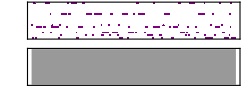

CellularAutomata-105_level7_BlackKeys_8.mid

```mathematica
snd8=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["CellularAutomata-105_level7_BlackKeys_8.mid",snd8]
```

```mathematica
wb={4*0.24,0.24,0.24,0.24,0.24,0.48,0.48,0.48,0.48,0.24,0.24,0.24,0.24,0.48,0.48};
```

```mathematica
Apply[Plus,wb]
```

5.76

```mathematica
snd4c=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["CellularAutomata-105_level7_BlackKeys_4c.mid",snd4c]
```

Sound[{SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.96,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[6,0.96,Piano],SoundNote[1,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[List,0.96,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.96,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[List,0.96,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.96,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.96,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.48,Piano],SoundNote[1,0.96,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.96,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.96,Piano],SoundNote[8,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[3,0.96,Piano],SoundNote[1,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.96,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.96,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.48,Piano],SoundNote[1,0.96,Piano],SoundNote[List,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.96,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.96,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.48,Piano],SoundNote[3,0.96,Piano],SoundNote[1,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[3,0.96,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.96,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.48,Piano],SoundNote[6,0.96,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[8,0.96,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.96,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[3,0.96,Piano],SoundNote[6,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.96,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.96,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.48,Piano],SoundNote[List,0.96,Piano],SoundNote[3,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[8,0.96,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.96,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[1,0.96,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[6,0.96,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[8,0.96,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[6,0.96,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[List,0.96,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.96,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.48,Piano],SoundNote[3,0.96,Piano],SoundNote[6,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[3,0.96,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.96,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[1,0.96,Piano],SoundNote[3,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[1,0.96,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.96,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.48,Piano],SoundNote[List,0.96,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[1,0.96,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.96,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.48,Piano],SoundNote[6,0.96,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.96,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.96,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.48,Piano],SoundNote[8,0.96,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.96,Piano]}]

SoundNote::invnote: "List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_4c.mid

```mathematica
snd5c=Sound[Table[SoundNote[PiDigits[[i]]-24,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["CellularAutomata-105_level7_BlackKeys_5c.mid",snd5c]
```

Sound[{SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.96,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-21,0.96,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-24+List,0.96,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.96,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.96,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.96,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.96,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.96,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.96,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-21,0.96,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-16,0.96,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-16,0.96,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-16,0.96,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-23,0.96,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.48,SynthBass2]}]

SoundNote::invnote: "-24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_5c.mid

```mathematica
Clear[wa,wb]
```

```mathematica
wa={0.12,0.12,0.12,0.12,0.24,0.24,0.48,0.48,0.24,0.24,0.24,0.24};
```

```mathematica
Apply[Plus,wa]
```

2.88

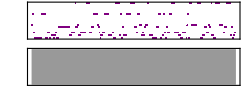

CellularAutomata-105_level7_BlackKeys_9.mid

```mathematica
snd9=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["CellularAutomata-105_level7_BlackKeys_9.mid",snd9]
```

```mathematica
wb={0.24,0.24,0.24,0.24,0.24,0.12,0.12,0.12,0.12,0.48,0.72,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wb]
```

3.36

```mathematica
snd4d=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["CellularAutomata-105_level7_BlackKeys_4d.mid",snd4d]
snd5d=Sound[Table[SoundNote[PiDigits[[i]]-24,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["CellularAutomata-105_level7_BlackKeys_5d.mid",snd5d]
```

Sound[{SoundNote[1,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[3,0.48,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.48,Piano],SoundNote[1,0.48,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[8,0.48,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.48,Piano],SoundNote[3,0.48,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.48,Piano],SoundNote[List,0.48,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[8,0.48,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.48,Piano],SoundNote[3,0.48,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.48,Piano],SoundNote[List,0.48,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[8,0.48,Piano],SoundNote[8,0.48,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[List,0.48,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[3,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.48,Piano],SoundNote[3,0.48,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[8,0.48,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[1,0.48,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[1,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[List,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.48,Piano],SoundNote[3,0.48,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.48,Piano],SoundNote[8,0.48,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.48,Piano],SoundNote[1,0.48,Piano],SoundNote[3,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[3,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[1,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[3,0.48,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[8,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[6,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.12,Piano],SoundNote[List,0.24,Piano],SoundNote[1,0.24,Piano],SoundNote[1,0.48,Piano],SoundNote[1,0.48,Piano],SoundNote[6,0.24,Piano],SoundNote[6,0.24,Piano],SoundNote[3,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[6,0.12,Piano],SoundNote[1,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.12,Piano],SoundNote[8,0.24,Piano],SoundNote[List,0.24,Piano],SoundNote[3,0.48,Piano],SoundNote[8,0.48,Piano],SoundNote[List,0.24,Piano]}]

SoundNote::invnote: "List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_4d.mid

Sound[{SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.72,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-23,0.72,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-21,0.72,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-24+List,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-23,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-24+List,0.72,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-24+List,0.48,SynthBass2],SoundNote[-24+List,0.72,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-23,0.48,SynthBass2],SoundNote[-18,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-21,0.48,SynthBass2],SoundNote[-16,0.72,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-24+List,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-16,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-24+List,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-16,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-16,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-18,0.48,SynthBass2],SoundNote[-18,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-23,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-18,0.24,SynthBass2],SoundNote[-21,0.24,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-18,0.12,SynthBass2],SoundNote[-23,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-16,0.48,SynthBass2],SoundNote[-16,0.72,SynthBass2],SoundNote[-24+List,0.12,SynthBass2],SoundNote[-21,0.12,SynthBass2],SoundNote[-16,0.12,SynthBass2],SoundNote[-24+List,0.12,SynthBass2]}]

SoundNote::invnote: "-24+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_5d.mid

```mathematica
wc={4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48,4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48};
```

```mathematica
Apply[Plus,wc]
```

13.44

```mathematica
w1={None,"Piano",None,"Piano",None,"Piano",None,"Piano",None,"Piano",None,"Piano",None,"Piano"};
```

```mathematica
snd4f=Sound[Table[SoundNote[{PiDigits[[i]]-5,PiDigits[[i]],PiDigits[[i]]+3},wc[[1+Mod[i,Length[wc]]]],w1[[1+Mod[i,8]]]],{i,Ceiling[Length[PiDigits]]/8}]]
Export["CellularAutomata-105_level7_BlackKeys_4f.mid",snd4f]
```

Sound[{SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{3,8,11},0.24,Piano],SoundNote[{-4,1,4},0.24,None],SoundNote[{-2,3,6},0.96,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-2,3,6},0.24,Piano],SoundNote[{-5+List,List,3+List},0.24,None],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-4,1,4},0.24,None],SoundNote[{3,8,11},0.24,Piano],SoundNote[{1,6,9},0.24,None],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-5+List,List,3+List},0.24,None],SoundNote[{-5+List,List,3+List},0.24,Piano],SoundNote[{-5+List,List,3+List},0.24,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-4,1,4},0.96,None],SoundNote[{-4,1,4},0.96,Piano],SoundNote[{1,6,9},0.24,None],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-5+List,List,3+List},0.24,Piano],SoundNote[{1,6,9},0.96,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{3,8,11},0.24,None],SoundNote[{3,8,11},0.24,Piano],SoundNote[{3,8,11},0.24,None]}]

SoundNote::invinst: "None" is not a valid style specification.

General::stop: Further output of SoundNote::invinst will be suppressed during this calculation.

SoundNote::invnote: "-5+List" is not a valid pitch specification.

SoundNote::invnote: "List" is not a valid pitch specification.

SoundNote::invnote: "3+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_4f.mid

```mathematica
snd5f=Sound[Table[SoundNote[{PiDigits[[i]]-5-12,PiDigits[[i]]-12,PiDigits[[i]]+3-12},wc[[1+Mod[i,Length[wc]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]/8}]]
Export["CellularAutomata-105_level7_BlackKeys_5f.mid",snd5f]
```

Sound[{SoundNote[{-16,-11,-8},0.24,SynthBass2],SoundNote[{-14,-9,-6},0.24,SynthBass2],SoundNote[{-9,-4,-1},0.24,SynthBass2],SoundNote[{-16,-11,-8},0.24,SynthBass2],SoundNote[{-14,-9,-6},0.96,SynthBass2],SoundNote[{-14,-9,-6},0.24,SynthBass2],SoundNote[{-14,-9,-6},0.24,SynthBass2],SoundNote[{-17+List,-12+List,-9+List},0.24,SynthBass2],SoundNote[{-11,-6,-3},0.24,SynthBass2],SoundNote[{-16,-11,-8},0.24,SynthBass2],SoundNote[{-9,-4,-1},0.24,SynthBass2],SoundNote[{-11,-6,-3},0.24,SynthBass2],SoundNote[{-11,-6,-3},0.24,SynthBass2],SoundNote[{-17+List,-12+List,-9+List},0.24,SynthBass2],SoundNote[{-17+List,-12+List,-9+List},0.24,SynthBass2],SoundNote[{-17+List,-12+List,-9+List},0.24,SynthBass2],SoundNote[{-16,-11,-8},0.24,SynthBass2],SoundNote[{-16,-11,-8},0.96,SynthBass2],SoundNote[{-16,-11,-8},0.96,SynthBass2],SoundNote[{-11,-6,-3},0.24,SynthBass2],SoundNote[{-11,-6,-3},0.24,SynthBass2],SoundNote[{-14,-9,-6},0.24,SynthBass2],SoundNote[{-17+List,-12+List,-9+List},0.24,SynthBass2],SoundNote[{-11,-6,-3},0.96,SynthBass2],SoundNote[{-16,-11,-8},0.24,SynthBass2],SoundNote[{-9,-4,-1},0.24,SynthBass2],SoundNote[{-9,-4,-1},0.24,SynthBass2],SoundNote[{-9,-4,-1},0.24,SynthBass2]}]

SoundNote::invnote: "-17+List" is not a valid pitch specification.

SoundNote::invnote: "-12+List" is not a valid pitch specification.

SoundNote::invnote: "-9+List" is not a valid pitch specification.

General::stop: Further output of SoundNote::invnote will be suppressed during this calculation.

CellularAutomata-105_level7_BlackKeys_5f.mid

```mathematica
(*end*)
```